# Table of Tables

```mathematica
Clear@tables
tables[n1_,n2_]:=Join@@Table[{a[i,j],b[i,j]},{i,n1},{j,0,n2}]
Short@tables[100,100]
```

```mathematica
Clear@tables2
tables2[n1_,n2_]:={a@##,b@##}&@@@Tuples@Range[{1,0},{n1,n2}]
```

```mathematica
With[
{n1=10,n2=20},
SameQ[
Join@@Table[{a[i,j],b[i,j]},{i,n1},{j,0,n2}],
{a@##,b@##}&@@@Tuples@Range[{1,0},{n1,n2}],
Replace[Tuples@Range[{1,0},{n1,n2}],{x__}:>{a[x],b[x]},1],
Tuples@Range[{1,0},{n1,n2}]/.{x__Integer}:>{a[x],b[x]},
Join@@Array[{a@##,b@##}&,{n1,n2+1},{1,0}]
]
]
```

```mathematica
Join@@Table[{i,j},{i,100},{j,0,100}]//Short//AbsoluteTiming
Tuples@Range[{1,0},{100,100}]//Short//AbsoluteTiming
%%⟦2⟧===%⟦2⟧
```

```mathematica
ClearSystemCache[]
DiscretePlot[
{
AbsoluteTiming[Join@@Table[{a[i,j],b[i,j]},{i,n},{j,0,n}]]⟦1⟧,
AbsoluteTiming[Join@@Array[{a@##,b@##}&,{n,n+1},{1,0}]]⟦1⟧,
AbsoluteTiming[{a@##,b@##}&@@@Tuples@Range[{1,0},{n,n}]]⟦1⟧,
AbsoluteTiming[Replace[Tuples@Range[{1,0},{n,n}],{x__}:>{a[x],b[x]},1]]⟦1⟧,
AbsoluteTiming[Tuples@Range[{1,0},{n,n}]/.{x__Integer}:>{a[x],b[x]}]⟦1⟧
},
{n,1,501,10},
Frame->True,
FrameLabel->{"List Length (n)","Timing (s)"},
Joined->True,
Filling->None,
PlotLegends->{"Table","Array","Apply","Replace","ReplaceAll"},
PlotLabel->"Method Timing Comparison \r",
ImageSize->Large,
BaseStyle->{12,FontFamily->Times}
]
```

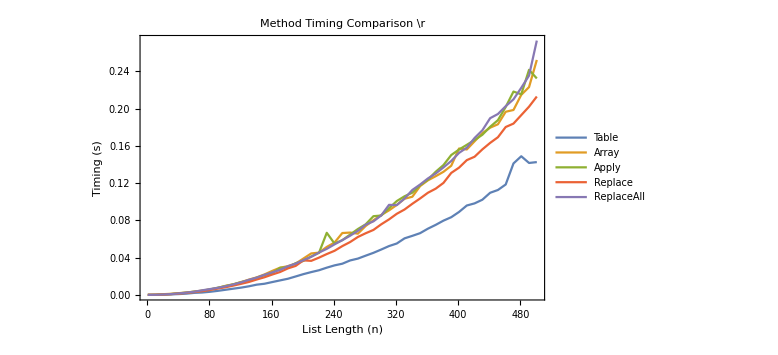
```mathematica
(*SetDirectory@StringReplace[Directory[],"Documents"->"Desktop"];Export["Timing_Comp.png",-Graphics-]*)
```